```mathematica
f[x_]:=(First[RealDigits[
N[x,5000],4]])/.{0->{1,0},1->{0,1},2->{-1,0},3->{0,-1}}//Accumulate//Line//Graphics
```

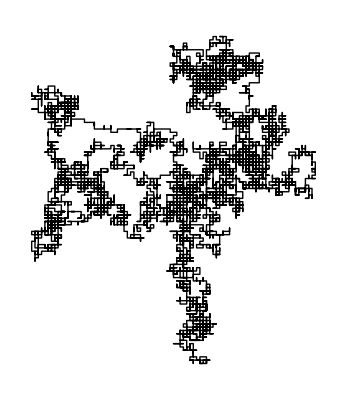
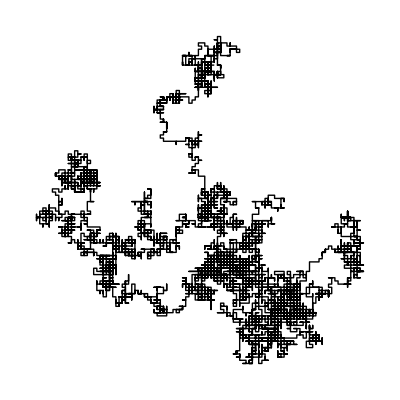
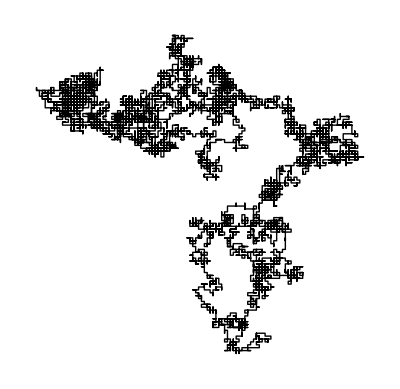
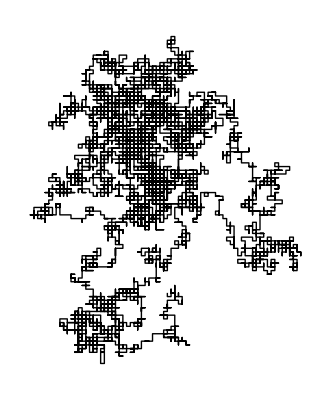
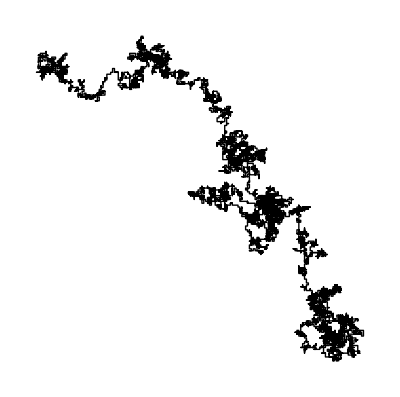
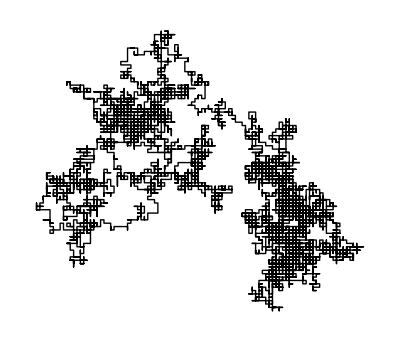
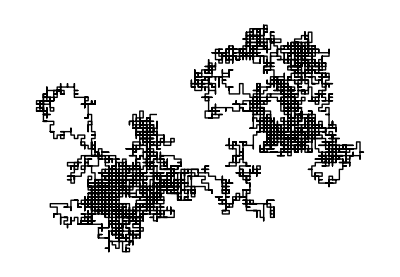
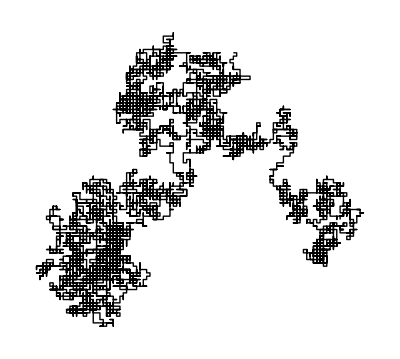
{π→-Graphics-,ⅇ→-Graphics-,GoldenRatio→-Graphics-,Log[2]→-Graphics-,ⅇ^π→-Graphics-,π^ⅇ→-Graphics-,ⅇ^ⅇ→-Graphics-,π^π→-Graphics-,ⅇ π→-Graphics-,ⅇ/π→-Graphics-,π/ⅇ→-Graphics-}

```mathematica
#->f[#]&/@{Pi,E,GoldenRatio,Log[2],E^Pi,Pi^E,E^E,Pi^Pi,Pi*E,E/Pi,Pi/E}
```